```mathematica
Fitness[q_,nu_,qs_]:=If [nu≠Infinity,Exp[(1/nu) Cos[2 Pi q- 2 Pi qs]]/( BesselI[0,1/nu]),1];
```

```mathematica
a = 0.5;
Q =0.25;
μ = 0.2;
qs = 0.5;
 
g[x_,nu_] :=Q a x/μ NIntegrate[ Fitness[qq, nu, qs]/(μ + a x Fitness[qq,nu,qs]),{qq,0,1}]
```

# Coexistence between generalist and specialits.

## Using NDSolve in Mathematica for the von Mises fitness

```mathematica
MeanField[com_,other_]:=Module[{NSP,B,μ,nstep,qstep,QQ,TMAX,aa,oldfitn,fitn,initialE,initialO, fE,fO,systemE,systemO,Fullsystem,variableE,variableO,Fullvariable,Solution, Result0,Result1,finalResult},
(* This is the parameter for species*)

NSP =Length[com];
(*
com[[i]] ={qS,nu, a};
land = {Qbar = B, mu, nqstep,TMAX}
*)

B = other[[1]];
μ = other[[2]];
nstep = other[[3]];
qstep = 1./nstep; QQ = Range[qstep,1,qstep];
TMAX = other[[4]];

aa= com[[All,3]];
Fitness[q_,spd_]:=If [spd[[2]]==Infinity,1. ,Exp[Cos[2 Pi (q- spd[[1]])]/spd[[2]]]/ BesselI[0,1/spd[[2]]]];

oldfitn =Table[Fitness[q, com[[sp]]],{sp,NSP},{q,QQ}];

fitn = Table[oldfitn[[sp]]/(qstep Total[oldfitn[[sp]]]),{sp,NSP}];
 (*Because of the discretization, the total fitness can be different, just renormalize here*)

(* Setting initial condition*)

initialE= Table[ρE[q][0]==0.1*B/μ,{q,QQ}];
initialO= Table[ρ[sp,q][0]== 0.9B/(μ NSP),{sp,NSP},{q,QQ}]; (* we assume 10 percent is empty, the rest ,90% is divided equally among the other species*)

(*This function calculates the change in abundance of resources of type q at time t that is empty (not occupied) *)
fE[q_,t_]:= B- μ* ρE[q][t]- ρE[q][t]* Sum[aa[[sp]]*fitn[[sp,Round[q/qstep]]]*  qstep* Sum[ρ[sp,qq][t],{qq,QQ}],{sp,NSP}];

(*This function calculates the change in the abundance of resources of type q at time t  that is occupied by species sp*)
fO[sp_,q_,t_]:=-μ * ρ[sp,q][t]+ρE[q][t]* aa[[sp]]*fitn[[sp,Round[q/qstep]]]* qstep*Sum[ρ[sp,qq][t],{qq,QQ}];


systemE=Table[ρE[q]'[t]==fE[q,t],{q,QQ}];
systemO=Table[ρ[sp,q]'[t]==fO[sp,q,t],{sp,NSP},{q,QQ}];

Fullsystem=Flatten[{systemE,systemO,initialE,initialO}];

variableE=Table[ρE[q],{q,QQ}];
variableO=Table[ρ[sp,q],{sp,NSP},{q,QQ}];

Fullvariable=Flatten[{variableE,variableO}];

Solution=NDSolve[Fullsystem,Fullvariable,{t,0,TMAX}];

(*This one is for the abundance at the middle of the simulation*)
Result0=Evaluate[Table[ρ[sp,q][TMAX/2.],{sp,NSP},{q,QQ}] /.Solution];

(*This one is for the abundance at the end of the simulation*)
Result1=Evaluate[Table[ρ[sp,q][TMAX],{sp,NSP},{q,QQ}] /.Solution];

finalResult= {Flatten[Result0,1],Flatten[Result1,1]}; 
finalResult]
```

```mathematica
localdir = "C:\\Users\\tramiada\\Documents\\Projects\\coexistence\\sim2\\";  qS1 = 0.25; qS2= 0.75; as =0.5;
NU= Flatten[{Subdivide[0.05,2,50],4,8,16}];

OTHER ={B = 2,μ = 0.1,NSTEP=100,TMAX = 1000};
time1= AbsoluteTiming[
Do[
OTHER ={B ,μ = 0.1,NSTEP=100,TMAX = 1000};
middata= enddata= {};
Do[
com1= {qS1,ν,as};
com2 = {qS2 ,ν, as};
com3 = {0.5 ,Infinity, ag};
COM = {com1,com2,com3};
data = MeanField2[COM,OTHER];

data1 = data[[1]]; (*this is prevelance at the middle of the simulation*)
data2= data[[2]];  (*this is prevelance at the end of the simulation*)

PrependTo[data1,ν];
PrependTo[data2,ν];

AppendTo[middata, data1];
AppendTo[enddata, data2];
,{ν,NU}];
Export[localdir<>"midTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_ag_"<>ToString@ag<>".csv",middata];
Export[localdir<>"endTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_ag_"<>ToString@ag<>".csv",enddata];
,{ag,as Subdivide[0.1,0.95,5]},{B,{1,2,4}}];
]; (* about 11 min*)
```

```mathematica
On[Assert];
```

```mathematica
MeanField3Species[com_,other_]:=Module[{(*NSP,B,μ,nstep,qstep,QQ,TMAX,aa,oldfitn,fitn,initialE,initialO, fE,fO,systemE,systemO,Fullsystem,variableE,variableO,Fullvariable,Solution, Result0,Result1,finalResult*)},
(* This is the parameter for species*)

NSP =Length[com];
Assert[NSP ==3];
(*
com[[i]] ={qS,nu, a};
land = {Qbar = B, mu, nqstep,TMAX}
*)

B = other[[1]];
μ = other[[2]];
nstep = other[[3]];
qstep = 1./nstep; QQ = Range[qstep,1,qstep];
TMAX = other[[4]];
z = other[[5]];

aa= com[[All,3]];
Fitness[q_,spd_]:=If [spd[[2]]==Infinity,1. ,Exp[Cos[2 Pi (q- spd[[1]])]/spd[[2]]]/ BesselI[0,1/spd[[2]]]];

oldfitn =Table[Fitness[q, com[[sp]]],{sp,NSP},{q,QQ}];

fitn = Table[oldfitn[[sp]]/(qstep Total[oldfitn[[sp]]]),{sp,NSP}];
 (*Because of the discretization, the total fitness can be different, just renormalize here*)
fE[q_,t_]:= B- μ* ρE[q][t]- ρE[q][t]* Sum[aa[[sp]]*fitn[[sp,Round[q/qstep]]]*  qstep* Sum[ρ[sp,qq][t],{qq,QQ}],{sp,NSP}];

(* Setting initial condition*)
occ = 0.01;
initialE= Table[ρE[q][0]==1 - 7occ B/μ,{q,QQ}];
initial1 = Table[ρ1[q][0]== occ B/(μ NSP),{q,QQ}];
initial2 = Table[ρ2[q][0]== occ B/(μ NSP),{q,QQ}];
initial3 = Table[ρ3[q][0]== occ B/(μ NSP),{q,QQ}];
initial12 = Table[ρ12[q][0]== occ B/(μ NSP),{q,QQ}];
initial13 = Table[ρ13[q][0]== occ B/(μ NSP),{q,QQ}];
initial23 = Table[ρ23[q][0]== occ B/(μ NSP),{q,QQ}];
initial123 = Table[ρ123[q][0]== occ B/(μ NSP),{q,QQ}];

 (* we assume 10 percent is empty, the rest ,90% is divided equally among the other species*)

(*This function calculates the change in abundance of resources of type q at time t that is empty (not occupied) *)
fE[q_,t_]:= B- μ* ρE[q][t] - ρE[q][t] (
aa[[1]] fitn[[1,Round[q/qstep]]] * qstep*Sum[ (ρ1[qq][t] +  ρ12[qq][t]+ ρ13[qq][t] + ρ123[qq][t]),{qq,QQ}] +
aa[[2]] fitn[[2,Round[q/qstep]]] * qstep*Sum[ (ρ2[qq][t] +  ρ12[qq][t]+ ρ23[qq][t] + ρ123[qq][t]),{qq,QQ}]+
aa[[3]] fitn[[3,Round[q/qstep]]] * qstep*Sum[ (ρ3[qq][t] +  ρ13[qq][t]+ ρ23[qq][t] + ρ123[qq][t]),{qq,QQ}]
);

(*This function calculates the change in the abundance of resources of type q at time t  that is occupied by species sp*)
f1[q_,t_]:= -μ * ρ1[q][t]
- ρ1[q][t] * z * (aa[[2]] fitn[[2,Round[q/qstep]]] * qstep* Sum[ (ρ2[qq][t] +  ρ12[qq][t]+ ρ23[qq][t] + ρ123[qq][t]),{qq,QQ}] + aa[[3]] fitn[[3,Round[q/qstep]]] * qstep* Sum[(ρ3[qq][t] +  ρ13[qq][t]+ ρ23[qq][t] + ρ123[qq][t]),{qq,QQ}])
+ 
(ρE[q][t])* aa[[1]]*fitn[[1,Round[q/qstep]]]* qstep*Sum[(ρ1[qq][t]+ ρ12[qq][t] +  ρ13[qq][t] + ρ123[qq][t]),{qq,QQ}];

f2[q_,t_]:=-μ * ρ2[q][t]
- ρ2[q][t] * z * (aa[[1]] fitn[[1,Round[q/qstep]]] * qstep*Sum[ (ρ1[qq][t] +  ρ12[qq][t]+ ρ13[qq][t] + ρ123[qq][t]),{qq,QQ}] + aa[[3]] fitn[[3,Round[q/qstep]]] * qstep*Sum[(ρ3[qq][t] +  ρ13[qq][t]+ ρ23[qq][t] + ρ123[qq][t]),{qq,QQ}])
+ 
(ρE[q][t])* aa[[2]]*fitn[[2,Round[q/qstep]]]* qstep*Sum[(ρ2[qq][t]+ ρ12[qq][t] +  ρ23[qq][t] + ρ123[qq][t]),{qq,QQ}];

f3[q_,t_]:=-μ * ρ3[q][t]- ρ3[q][t] * z * (aa[[1]] fitn[[1,Round[q/qstep]]] * qstep* Sum[(ρ1[qq][t] +  ρ12[qq][t]+ ρ13[qq][t] + ρ123[qq][t]),{qq,QQ}] + aa[[2]] fitn[[2,Round[q/qstep]]] * qstep* Sum[(ρ2[qq][t] +  ρ12[qq][t]+ ρ23[qq][t] + ρ123[qq][t]),{qq,QQ}])
+ 
(ρE[q][t])* aa[[3]]*fitn[[3,Round[q/qstep]]]* qstep*Sum[(ρ3[qq][t]+ ρ13[qq][t] +  ρ23[qq][t] + ρ123[qq][t]),{qq,QQ}];

f12[q_,t_]:=-μ * ρ12[q][t]
- ρ12[q][t] * z^2 * (aa[[3]] fitn[[3,Round[q/qstep]]] * qstep* Sum[ (ρ3[qq][t] +  ρ13[qq][t]+ ρ23[qq][t] + ρ123[qq][t]),{qq,QQ}])
+ 
(ρ2[q][t])* z *aa[[1]]*fitn[[1,Round[q/qstep]]]* qstep*Sum[(ρ1[qq][t]+ ρ12[qq][t] +  ρ13[qq][t] + ρ123[qq][t]),{qq,QQ}] + (ρ1[q][t])* z* aa[[2]]*fitn[[2,Round[q/qstep]]]* qstep*Sum[(ρ2[qq][t]+ ρ12[qq][t] +  ρ23[qq][t] + ρ123[qq][t]),{qq,QQ}] ;

f13[q_,t_]:=-μ * ρ13[q][t]
- ρ13[q][t] * z^2 * (aa[[2]] fitn[[2,Round[q/qstep]]] * qstep* Sum[ (ρ2[qq][t] +  ρ12[qq][t]+ ρ23[qq][t] + ρ123[qq][t]),{qq,QQ}])
+ 
(ρ3[q][t])* z * aa[[1]]*fitn[[1,Round[q/qstep]]]* qstep*Sum[(ρ1[qq][t]+ ρ12[qq][t] +  ρ13[qq][t] + ρ123[qq][t]),{qq,QQ}] + (ρ1[q][t])* z * aa[[3]]*fitn[[3,Round[q/qstep]]]* qstep*Sum[(ρ3[qq][t]+ ρ13[qq][t] +  ρ23[qq][t] + ρ123[qq][t]),{qq,QQ}] ;

f23[q_,t_]:=-μ * ρ23[q][t]
- ρ23[q][t] * z^2 * (aa[[1]] fitn[[1,Round[q/qstep]]] *qstep* Sum[ (ρ1[qq][t] +  ρ12[qq][t]+ ρ13[qq][t] + ρ123[qq][t]),{qq,QQ}])
+ 
(ρ2[q][t])* z * aa[[3]]*fitn[[3,Round[q/qstep]]]* qstep*Sum[(ρ3[qq][t]+ ρ13[qq][t] +  ρ23[qq][t] + ρ123[qq][t]),{qq,QQ}] + (ρ3[q][t])* z * aa[[2]]*fitn[[2,Round[q/qstep]]]* qstep*Sum[(ρ2[qq][t]+ ρ12[qq][t] +  ρ23[qq][t] + ρ123[qq][t]),{qq,QQ}] ;

f123[q_,t_]:=-μ * ρ123[q][t]
+ 
(ρ12[q][t])* z^2 * aa[[3]]*fitn[[3,Round[q/qstep]]]* qstep*Sum[(ρ3[qq][t]+ ρ13[qq][t] +  ρ23[qq][t] + ρ123[qq][t]),{qq,QQ}] + (ρ13[q][t])* z^2 * aa[[2]]*fitn[[2,Round[q/qstep]]]* qstep*Sum[(ρ2[qq][t]+ ρ12[qq][t] +  ρ23[qq][t] + ρ123[qq][t]),{qq,QQ}] +
(ρ23[q][t])* z^2 * aa[[1]]*fitn[[1,Round[q/qstep]]]* qstep*Sum[(ρ1[qq][t]+ ρ12[qq][t] +  ρ13[qq][t] + ρ123[qq][t]),{qq,QQ}];


systemE=Table[ρE[q]'[t]==fE[q,t],{q,QQ}];

system1=Table[ρ1[q]'[t]==f1[q,t],{q,QQ}];
system2=Table[ρ2[q]'[t]==f2[q,t],{q,QQ}];
system3=Table[ρ3[q]'[t]==f3[q,t],{q,QQ}];

system12=Table[ρ12[q]'[t]==f12[q,t],{q,QQ}];
system13=Table[ρ13[q]'[t]==f13[q,t],{q,QQ}];
system23=Table[ρ23[q]'[t]==f23[q,t],{q,QQ}];

system123=Table[ρ123[q]'[t]==f123[q,t],{q,QQ}];


Fullsystem=Flatten[{systemE,system1 ,system2, system3, system12, system13, system23, system123,initialE,initial1, initial2,initial3,initial12, initial13,initial23,initial123}];

variableE=Table[ρE[q],{q,QQ}];

variable1=Table[ρ1[q],{q,QQ}];
variable2=Table[ρ2[q],{q,QQ}];
variable3=Table[ρ3[q],{q,QQ}];

variable12=Table[ρ12[q],{q,QQ}];
variable13=Table[ρ13[q],{q,QQ}];
variable23=Table[ρ23[q],{q,QQ}];

variable123=Table[ρ123[q],{q,QQ}];


Fullvariable=Flatten[{variableE,variable1, variable2, variable3, variable12, variable13, variable23, variable123}];

Solution=NDSolve[Fullsystem,Fullvariable,{t,0,TMAX}];

(*This one is for the abundance at the middle of the simulation*)
midE=Evaluate[Table[ρE[q][TMAX/2.],{q,QQ}] /.Solution];

mid1=Evaluate[Table[ρ1[q][TMAX/2.],{q,QQ}] /.Solution];
mid2=Evaluate[Table[ρ2[q][TMAX/2.],{q,QQ}] /.Solution];
mid3=Evaluate[Table[ρ3[q][TMAX/2.],{q,QQ}] /.Solution];

mid12=Evaluate[Table[ρ12[q][TMAX/2.],{q,QQ}] /.Solution];
mid13=Evaluate[Table[ρ13[q][TMAX/2.],{q,QQ}] /.Solution];
mid23=Evaluate[Table[ρ23[q][TMAX/2.],{q,QQ}] /.Solution];

mid123=Evaluate[Table[ρ123[q][TMAX/2.],{q,QQ}] /.Solution];

fmid = {Flatten[midE,1],Flatten[mid1,1],Flatten[mid2,1],Flatten[mid3,1],Flatten[mid12,1],Flatten[mid13,1],Flatten[mid23,1],Flatten[mid123,1]};

(*This one is for the abundance at the end of the simulation*)

finE=Evaluate[Table[ρE[q][TMAX],{q,QQ}] /.Solution];

fin1=Evaluate[Table[ρ1[q][TMAX],{q,QQ}] /.Solution];
fin2=Evaluate[Table[ρ2[q][TMAX],{q,QQ}] /.Solution];
fin3=Evaluate[Table[ρ3[q][TMAX],{q,QQ}] /.Solution];

fin12=Evaluate[Table[ρ12[q][TMAX],{q,QQ}] /.Solution];
fin13=Evaluate[Table[ρ13[q][TMAX],{q,QQ}] /.Solution];
fin23=Evaluate[Table[ρ23[q][TMAX],{q,QQ}] /.Solution];

fin123=Evaluate[Table[ρ123[q][TMAX],{q,QQ}] /.Solution];

ffin = {Flatten[finE,1],Flatten[fin1,1],Flatten[fin2,1],Flatten[fin3,1],Flatten[fin12,1],Flatten[fin13,1],Flatten[fin23,1],Flatten[fin123,1]};

finalResult= {fmid,ffin}; 
finalResult]
```

```mathematica
qS1 = 0.25;qS2 = 0.75; ν = 0.25; as = 0.5;
com  = {{qS1,ν, as},{qS2,ν, as},{1.,Infinity, 0.8as}};OTHER ={B = 2,μ = 0.1,NSTEP=100,TMAX = 1000,z =0.1};
out =MeanField3Species[com,OTHER];
```

```mathematica
ps = {Red, Green, Blue, Yellow,Magenta,Cyan, Black};
```

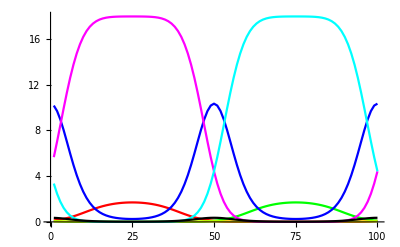

```mathematica
ListPlot[out[[1,2;;]],Joined->True, PlotStyle->ps,PlotRange->All]
```

#### For fixed ag

```mathematica
as= 0.5;
AG  =as Subdivide[0.1,0.95,5];
OTHER ={B = 1,μ = 0.1,NSTEP=100,TMAX = 2000};
```

```mathematica
FIG ={};
Do[
data0= ToExpression@Import[localdir<>"midTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_ag_"<>ToString@ag<>".csv"];

data1= ToExpression@Import[localdir<>"endTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_ag_"<>ToString@ag<>".csv"];
FIG= {};
Do[

dd = data0[[i]];
sp1 = Transpose[{Subdivide[0.,1,NSTEP-1],dd[[2]]}];
sp2 = Transpose[{Subdivide[0.,1,NSTEP-1],dd[[3]]}];
sp3 = Transpose[{Subdivide[0.,1,NSTEP-1],dd[[4]]}];

ee = data1[[i]];
sp1f = Transpose[{Subdivide[0.,1,NSTEP-1],ee[[2]]}];
sp2f = Transpose[{Subdivide[0.,1,NSTEP-1],ee[[3]]}];
sp3f = Transpose[{Subdivide[0.,1,NSTEP-1],ee[[4]]}];
fig =Labeled[ListLinePlot[{sp1,sp2,sp3,sp1f,sp2f,sp3f},PlotStyle->{Pink,Cyan,{Black,Dashed},Red,Blue,{Gray,Dashed}},PlotRange->{All,{0,B/μ}}],ToString@dd[[1]], Top];
AppendTo[FIG,fig];
,{i,Length[NU]}];

,{ag,{AG[[5]]}}];
```

```mathematica
Manipulate[FIG[[i]],{i,1,Length[NU],1}]
```

Part::partd: Part specification FIG ⟦ 7 ⟧ is longer than depth of object.

```mathematica
as= 0.5;
AG  =as Subdivide[0.1,0.95,5];
OTHER ={B = 4,μ = 0.1,NSTEP=100,TMAX = 2000};
```

```mathematica
FIG2 ={};
Do[
data0= ToExpression@Import[localdir<>"midTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_ag_"<>ToString@ag<>".csv"];

data1= ToExpression@Import[localdir<>"endTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_ag_"<>ToString@ag<>".csv"];
FIG= {};
Do[

dd = data0[[i]];
sp1 = Transpose[{Subdivide[0.,1,NSTEP-1],dd[[2]]}];
sp2 = Transpose[{Subdivide[0.,1,NSTEP-1],dd[[3]]}];
sp3 = Transpose[{Subdivide[0.,1,NSTEP-1],dd[[4]]}];

ee = data1[[i]];
sp1f = Transpose[{Subdivide[0.,1,NSTEP-1],ee[[2]]}];
sp2f = Transpose[{Subdivide[0.,1,NSTEP-1],ee[[3]]}];
sp3f = Transpose[{Subdivide[0.,1,NSTEP-1],ee[[4]]}];
fig =Labeled[ListLinePlot[{sp1,sp2,sp3,sp1f,sp2f,sp3f},PlotStyle->{Pink,Cyan,{Black,Dashed},Red,Blue,{Gray,Dashed}},PlotRange->{All,{0,B/μ}}],ToString@dd[[1]], Top];
AppendTo[FIG2,fig];
,{i,Length[NU]}];

,{ag,{AG[[5]]}}];
```

```mathematica
Manipulate[FIG2[[i]],{i,1,Length[NU],1}]
```

Part::partd: Part specification FIG2 ⟦ 7 ⟧ is longer than depth of object.

```mathematica
FIG ={};Do[data0= ToExpression@Import["C:\\Users\\tramiada\\Documents\\Projects\\coexistence\\sim2\\midTMAX_NSTEP_100_ag_"<>ToString@ag<>".csv"];

data1= ToExpression@Import["C:\\Users\\tramiada\\Documents\\Projects\\coexistence\\sim2\\endTMAX_NSTEP_100_ag_"<>ToString@ag<>".csv"];

dd = data0[[50]];
sp1 = Transpose[{Subdivide[0.,1,99],dd[[2]]}];
sp2 = Transpose[{Subdivide[0.,1,99],dd[[3]]}];
sp3 = Transpose[{Subdivide[0.,1,99],dd[[4]]}];

ee = data1[[50]];
sp1f = Transpose[{Subdivide[0.,1,99],ee[[2]]}];
sp2f = Transpose[{Subdivide[0.,1,99],ee[[3]]}];
sp3f = Transpose[{Subdivide[0.,1,99],ee[[4]]}];
fig =Labeled[ListLinePlot[{sp1,sp2,sp3,sp1f,sp2f,sp3f},PlotStyle->{Pink,Cyan,{Black,Dashed},Red,Blue,{Gray,Dashed}},PlotRange->{All,{0,B/μ}}],ToString@ag, Top];

AppendTo[FIG,fig];

,{ag,as Subdivide[0.1,0.95,10]}];
```

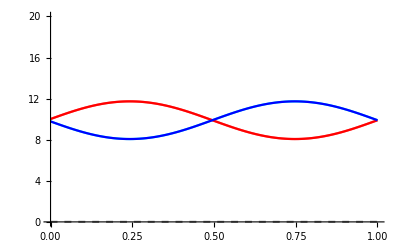
{-Graphics-0.05,-Graphics-0.0925,-Graphics-0.135,-Graphics-0.1775,-Graphics-0.22,-Graphics-0.2625,-Graphics-0.305,-Graphics-0.3475,-Graphics-0.39,-Graphics-0.4325,-Graphics-0.475}

```mathematica
FIG
```

# Recycling

```mathematica
MeanField3Species[com_,other_]:=Module[{(*NSP,B,μ,nstep,qstep,QQ,TMAX,aa,oldfitn,fitn,initialE,initialO, fE,fO,systemE,systemO,Fullsystem,variableE,variableO,Fullvariable,Solution, Result0,Result1,finalResult*)},
(* This is the parameter for species*)

NSP =Length[com];
Assert[NSP ==3];
(*
com[[i]] ={qS,nu, a};
land = {Qbar = B, mu, nqstep,TMAX}
*)

B = other[[1]];
μ = other[[2]];
nstep = other[[3]];
qstep = 1./nstep; QQ = Range[qstep,1,qstep];
TMAX = other[[4]];
z = other[[5]];

aa= com[[All,3]];
Fitness[q_,spd_]:=If [spd[[2]]==Infinity,1. ,Exp[Cos[2 Pi (q- spd[[1]])]/spd[[2]]]/ BesselI[0,1/spd[[2]]]];

oldfitn =Table[Fitness[q, com[[sp]]],{sp,NSP},{q,QQ}];

fitn = Table[oldfitn[[sp]]/(qstep Total[oldfitn[[sp]]]),{sp,NSP}];
 (*Because of the discretization, the total fitness can be different, just renormalize here*)

(* Setting initial condition*)
occ = 0.01;
initialR= Table[ρR[q][0]==B/μ,{q,QQ}];
initial1 = Table[ρ1[q][0]== occ B/(μ NSP),{q,QQ}];
initial2 = Table[ρ2[q][0]== occ B/(μ NSP),{q,QQ}];
initial3 = Table[ρ3[q][0]== occ B/(μ NSP),{q,QQ}];
initial12 = Table[ρ12[q][0]== occ B/(μ NSP),{q,QQ}];
initial13 = Table[ρ13[q][0]== occ B/(μ NSP),{q,QQ}];
initial23 = Table[ρ23[q][0]== occ B/(μ NSP),{q,QQ}];
initial123 = Table[ρ123[q][0]== occ B/(μ NSP),{q,QQ}];

 (* we assume 10 percent is empty, the rest ,90% is divided equally among the other species*)

(*This function calculates the change in abundance of resources of type q at time t that is empty (not occupied) *)
fR[q_,t_]:= B- μ* ρR[q][t];

(*This function calculates the change in the abundance of resources of type q at time t  that is occupied by species sp*)
f1[q_,t_]:= -μ * ρ1[q][t]
- ρ1[q][t] * z * (aa[[2]] fitn[[2,Round[q/qstep]]] * qstep* Sum[ (ρ2[qq][t] +  ρ12[qq][t]+ ρ23[qq][t] + ρ123[qq][t]),{qq,QQ}] + aa[[3]] fitn[[3,Round[q/qstep]]] * qstep* Sum[(ρ3[qq][t] +  ρ13[qq][t]+ ρ23[qq][t] + ρ123[qq][t]),{qq,QQ}])
+ 
(ρR[q][t] - (ρ1[q][t] + ρ2[q][t] + ρ3[q][t] + ρ12[q][t]+ ρ13[q][t] + ρ23[q][t]+ ρ123[q][t]))* aa[[1]]*fitn[[1,Round[q/qstep]]]* qstep*Sum[(ρ1[qq][t]+ ρ12[qq][t] +  ρ13[qq][t] + ρ123[qq][t]),{qq,QQ}];

f2[q_,t_]:=-μ * ρ2[q][t]
- ρ2[q][t] * z * (aa[[1]] fitn[[1,Round[q/qstep]]] * qstep*Sum[ (ρ1[qq][t] +  ρ12[qq][t]+ ρ13[qq][t] + ρ123[qq][t]),{qq,QQ}] + aa[[3]] fitn[[3,Round[q/qstep]]] * qstep*Sum[(ρ3[qq][t] +  ρ13[qq][t]+ ρ23[qq][t] + ρ123[qq][t]),{qq,QQ}])
+ 
(ρR[q][t] - (ρ1[q][t] + ρ2[q][t] + ρ3[q][t] + ρ12[q][t]+ ρ13[q][t] + ρ123[q][t]))* aa[[2]]*fitn[[2,Round[q/qstep]]]* qstep*Sum[(ρ2[qq][t]+ ρ12[qq][t] +  ρ23[qq][t] + ρ123[qq][t]),{qq,QQ}];

f3[q_,t_]:=-μ * ρ3[q][t]- ρ3[q][t] * z * (aa[[1]] fitn[[1,Round[q/qstep]]] * qstep* Sum[(ρ1[qq][t] +  ρ12[qq][t]+ ρ13[qq][t] + ρ123[qq][t]),{qq,QQ}] + aa[[2]] fitn[[2,Round[q/qstep]]] * qstep* Sum[(ρ2[qq][t] +  ρ12[qq][t]+ ρ23[qq][t] + ρ123[qq][t]),{qq,QQ}])
+ 
(ρR[q][t] - (ρ1[q][t] + ρ2[q][t] + ρ3[q][t] + ρ12[q][t]+ ρ13[q][t] + ρ123[q][t]))* aa[[3]]*fitn[[3,Round[q/qstep]]]* qstep*Sum[(ρ3[qq][t]+ ρ13[qq][t] +  ρ23[qq][t] + ρ123[qq][t]),{qq,QQ}];

f12[q_,t_]:=-μ * ρ12[q][t]
- ρ12[q][t] * z^2 * (aa[[3]] fitn[[3,Round[q/qstep]]] * qstep* Sum[ (ρ3[qq][t] +  ρ13[qq][t]+ ρ23[qq][t] + ρ123[qq][t]),{qq,QQ}])
+ 
(ρ2[q][t])* z *aa[[1]]*fitn[[1,Round[q/qstep]]]* qstep*Sum[(ρ1[qq][t]+ ρ12[qq][t] +  ρ13[qq][t] + ρ123[qq][t]),{qq,QQ}] + (ρ1[q][t])* z* aa[[2]]*fitn[[2,Round[q/qstep]]]* qstep*Sum[(ρ2[qq][t]+ ρ12[qq][t] +  ρ23[qq][t] + ρ123[qq][t]),{qq,QQ}] ;

f13[q_,t_]:=-μ * ρ13[q][t]
- ρ13[q][t] * z^2 * (aa[[2]] fitn[[2,Round[q/qstep]]] * qstep* Sum[ (ρ2[qq][t] +  ρ12[qq][t]+ ρ23[qq][t] + ρ123[qq][t]),{qq,QQ}])
+ 
(ρ3[q][t])* z * aa[[1]]*fitn[[1,Round[q/qstep]]]* qstep*Sum[(ρ1[qq][t]+ ρ12[qq][t] +  ρ13[qq][t] + ρ123[qq][t]),{qq,QQ}] + (ρ1[q][t])* z * aa[[3]]*fitn[[3,Round[q/qstep]]]* qstep*Sum[(ρ3[qq][t]+ ρ13[qq][t] +  ρ23[qq][t] + ρ123[qq][t]),{qq,QQ}] ;

f23[q_,t_]:=-μ * ρ23[q][t]
- ρ23[q][t] * z^2 * (aa[[1]] fitn[[1,Round[q/qstep]]] *qstep* Sum[ (ρ1[qq][t] +  ρ12[qq][t]+ ρ13[qq][t] + ρ123[qq][t]),{qq,QQ}])
+ 
(ρ2[q][t])* z * aa[[3]]*fitn[[3,Round[q/qstep]]]* qstep*Sum[(ρ3[qq][t]+ ρ13[qq][t] +  ρ23[qq][t] + ρ123[qq][t]),{qq,QQ}] + (ρ3[q][t])* z * aa[[2]]*fitn[[2,Round[q/qstep]]]* qstep*Sum[(ρ2[qq][t]+ ρ12[qq][t] +  ρ23[qq][t] + ρ123[qq][t]),{qq,QQ}] ;

f123[q_,t_]:=-μ * ρ123[q][t]
+ 
(ρ12[q][t])* z^2 * aa[[3]]*fitn[[3,Round[q/qstep]]]* qstep*Sum[(ρ3[qq][t]+ ρ13[qq][t] +  ρ23[qq][t] + ρ123[qq][t]),{qq,QQ}] + (ρ13[q][t])* z^2 * aa[[2]]*fitn[[2,Round[q/qstep]]]* qstep*Sum[(ρ2[qq][t]+ ρ12[qq][t] +  ρ23[qq][t] + ρ123[qq][t]),{qq,QQ}] +
(ρ23[q][t])* z^2 * aa[[1]]*fitn[[1,Round[q/qstep]]]* qstep*Sum[(ρ1[qq][t]+ ρ12[qq][t] +  ρ13[qq][t] + ρ123[qq][t]),{qq,QQ}];


systemR=Table[ρR[q]'[t]==fR[q,t],{q,QQ}];

system1=Table[ρ1[q]'[t]==f1[q,t],{q,QQ}];
system2=Table[ρ2[q]'[t]==f2[q,t],{q,QQ}];
system3=Table[ρ3[q]'[t]==f3[q,t],{q,QQ}];

system12=Table[ρ12[q]'[t]==f12[q,t],{q,QQ}];
system13=Table[ρ13[q]'[t]==f13[q,t],{q,QQ}];
system23=Table[ρ23[q]'[t]==f23[q,t],{q,QQ}];

system123=Table[ρ123[q]'[t]==f123[q,t],{q,QQ}];


Fullsystem=Flatten[{systemR,system1 ,system2, system3, system12, system13, system23, system123,initialR,initial1, initial2,initial3,initial12, initial13,initial23,initial123}];

variableR=Table[ρR[q],{q,QQ}];

variable1=Table[ρ1[q],{q,QQ}];
variable2=Table[ρ2[q],{q,QQ}];
variable3=Table[ρ3[q],{q,QQ}];

variable12=Table[ρ12[q],{q,QQ}];
variable13=Table[ρ13[q],{q,QQ}];
variable23=Table[ρ23[q],{q,QQ}];

variable123=Table[ρ123[q],{q,QQ}];


Fullvariable=Flatten[{variableR,variable1, variable2, variable3, variable12, variable13, variable23, variable123}];

Solution=NDSolve[Fullsystem,Fullvariable,{t,0,TMAX}];

(*This one is for the abundance at the middle of the simulation*)
midR=Evaluate[Table[ρR[q][TMAX/2.],{q,QQ}] /.Solution];

mid1=Evaluate[Table[ρ1[q][TMAX/2.],{q,QQ}] /.Solution];
mid2=Evaluate[Table[ρ2[q][TMAX/2.],{q,QQ}] /.Solution];
mid3=Evaluate[Table[ρ3[q][TMAX/2.],{q,QQ}] /.Solution];

mid12=Evaluate[Table[ρ12[q][TMAX/2.],{q,QQ}] /.Solution];
mid13=Evaluate[Table[ρ13[q][TMAX/2.],{q,QQ}] /.Solution];
mid23=Evaluate[Table[ρ23[q][TMAX/2.],{q,QQ}] /.Solution];

mid123=Evaluate[Table[ρ123[q][TMAX/2.],{q,QQ}] /.Solution];

fmid = {Flatten[midR,1],Flatten[mid1,1],Flatten[mid2,1],Flatten[mid3,1],Flatten[mid12,1],Flatten[mid13,1],Flatten[mid23,1],Flatten[mid123,1]};

(*This one is for the abundance at the end of the simulation*)

finR=Evaluate[Table[ρR[q][TMAX],{q,QQ}] /.Solution];

fin1=Evaluate[Table[ρ1[q][TMAX],{q,QQ}] /.Solution];
fin2=Evaluate[Table[ρ2[q][TMAX],{q,QQ}] /.Solution];
fin3=Evaluate[Table[ρ3[q][TMAX],{q,QQ}] /.Solution];

fin12=Evaluate[Table[ρ12[q][TMAX],{q,QQ}] /.Solution];
fin13=Evaluate[Table[ρ13[q][TMAX],{q,QQ}] /.Solution];
fin23=Evaluate[Table[ρ23[q][TMAX],{q,QQ}] /.Solution];

fin123=Evaluate[Table[ρ123[q][TMAX],{q,QQ}] /.Solution];

ffin = {Flatten[finR,1],Flatten[fin1,1],Flatten[fin2,1],Flatten[fin3,1],Flatten[fin12,1],Flatten[fin13,1],Flatten[fin23,1],Flatten[fin123,1]};

finalResult= {fmid,ffin}; 
finalResult]
```

```mathematica
qS1 = 0.3;qS2 = 0.6; ν = 0.5; as = 0.5;
com  = {{qS1,ν, as},{qS2,ν, as},{0.9,ν, as}};OTHER ={B = 2,μ = 0.1,NSTEP=40,TMAX = 100,z =0.1};
```

```mathematica
out =MeanField3Species[com,OTHER];
```

```mathematica
out[[2]]
```

{{20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.},{-6.94017×10^-17,-7.25415×10^-17,-4.91983×10^-17,5.52835×10^-17,3.59021×10^-16,1.08719×10^-15,2.6172×10^-15,5.39045×10^-15,9.23746×10^-15,1.21681×10^-14,1.17702×10^-14,8.83337×10^-15,5.66196×10^-15,3.30697×10^-15,1.79944×10^-15,8.93576×10^-16,3.64435×10^-16,6.27797×10^-17,-1.01631×10^-16,-1.85196×10^-16,-2.25587×10^-16,-2.481×10^-16,-2.69502×10^-16,-3.021×10^-16,-3.57911×10^-16,-4.52129×10^-16,-6.022×10^-16,-8.06797×10^-16,-9.80181×10^-16,-9.38077×10^-16,-6.65005×10^-16,-3.86566×10^-16,-2.16334×10^-16,-1.29508×10^-16,-8.66365×10^-17,-6.54762×10^-17,-5.57365×10^-17,-5.29073×10^-17,-5.50833×10^-17,-6.12468×10^-17},{0.0332907,0.042157,0.0620575,0.105093,0.201688,0.429526,0.984288,2.30908,5.10394,9.52316,14.0479,17.0619,18.5867,19.2814,19.5983,19.7497,19.8261,19.8656,19.8849,19.891,19.8856,19.8668,19.8277,19.7518,19.6006,19.284,18.5895,17.0648,14.0504,9.52479,5.10471,2.30937,0.984389,0.429562,0.201701,0.105099,0.0620597,0.0421579,0.0332911,0.0307499},{19.8852,19.866,19.8265,19.7502,19.5986,19.2816,18.5868,17.062,14.048,9.52316,5.10393,2.30908,0.984281,0.429521,0.201685,0.105091,0.0620561,0.0421561,0.0332903,0.0307498,0.0332913,0.0421586,0.0620613,0.105102,0.201709,0.42958,0.984432,2.30946,5.10483,9.52479,14.0501,17.0641,18.5887,19.2832,19.5999,19.7511,19.8272,19.8665,19.8854,19.891},{-2.83961×10^-17,-3.34159×10^-17,-2.75236×10^-17,4.03265×10^-17,3.64193×10^-16,1.62255×10^-15,6.02189×10^-15,1.98213×10^-14,5.55981×10^-14,1.21239×10^-13,1.94343×10^-13,2.4084×10^-13,1.12838×10^-13,-1.08968×10^-12,-1.86059×10^-12,-1.28856×10^-12,-6.85643×10^-13,-6.94969×10^-14,-1.22695×10^-14,-4.73238×10^-14,-5.48037×10^-14,-5.36043×10^-14,-4.80734×10^-14,-4.13857×10^-14,-3.52734×10^-14,-3.02898×10^-14,-2.61672×10^-14,-2.19301×10^-14,-1.6261×10^-14,-9.38055×10^-15,-4.00833×10^-15,-1.42207×10^-15,-4.97827×10^-16,-1.93293×10^-16,-8.78866×10^-17,-4.77618×10^-17,-3.11825×10^-17,-2.43719×10^-17,-2.25378×10^-17,-2.40808×10^-17},{-8.21956×10^-15,7.50646×10^-14,8.93678×10^-14,-8.32145×10^-14,-3.73185×10^-13,-3.55294×10^-13,5.33503×10^-14,1.429×10^-13,1.5595×10^-13,1.26642×10^-13,7.23703×10^-14,3.33032×10^-14,1.36191×10^-14,6.82035×10^-15,1.76408×10^-15,4.6059×10^-16,3.73858×10^-16,-3.73153×10^-17,-9.23808×10^-17,-8.77946×10^-17,-1.37333×10^-16,-1.054×10^-16,-1.67784×10^-16,-2.2406×10^-16,-3.42855×10^-16,-6.54047×10^-16,-1.37691×10^-15,-2.98482×10^-15,-5.88231×10^-15,-9.38552×10^-15,-1.08916×10^-14,-1.0509×10^-14,-9.29424×10^-15,-8.76184×10^-15,-8.53928×10^-15,-9.10328×10^-15,-9.80064×10^-15,-1.16262×10^-14,-1.32377×10^-14,-1.53028×10^-14},{9.85521×10^9,8.77465×10^9,8.21539×10^9,8.11318×10^9,8.47075×10^9,9.35642×10^9,1.08858×10^10,1.30918×10^10,1.54854×10^10,1.663×10^10,1.54853×10^10,1.30917×10^10,1.08857×10^10,9.35626×10^9,8.47055×10^9,8.11293×10^9,8.21511×10^9,8.77438×10^9,9.85501×10^9,1.15968×10^10,1.42367×10^10,1.81463×10^10,2.38909×10^10,3.23166×10^10,4.46692×10^10,6.27002×10^10,8.8461×10^10,1.22523×10^11,1.57962×10^11,1.74619×10^11,1.57956×10^11,1.22516×10^11,8.84553×10^10,6.26963×10^10,4.46667×10^10,3.2315×10^10,2.38899×10^10,1.81458×10^10,1.42366×10^10,1.15969×10^10},{0.000133685,0.000283851,0.000472057,0.000685548,0.000895157,0.00107108,0.00120041,0.00128704,0.00134069,0.00136935,0.00137782,0.0013683,0.00134069,0.00129194,0.00121476,0.00109679,0.000923488,0.000687525,0.000399917,0.0000894102,-0.000212574,-0.000487193,-0.000732788,-0.000961133,-0.00119139,-0.00144338,-0.00172508,-0.00200293,-0.002162,-0.00205018,-0.00167313,-0.00122647,-0.000862982,-0.000609297,-0.000438117,-0.000318679,-0.000228197,-0.00015036,-0.0000721501,0.0000185067}}

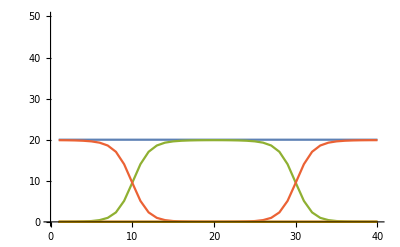

```mathematica
ListPlot[out[[2]],Joined->True]
```

```mathematica
MeanField3Species[com_,other_]:=Module[{(*NSP,B,μ,nstep,qstep,QQ,TMAX,aa,oldfitn,fitn,initialE,initialO, fE,fO,systemE,systemO,Fullsystem,variableE,variableO,Fullvariable,Solution, Result0,Result1,finalResult*)},
(* This is the parameter for species*)

NSP =Length[com];
Assert[NSP ==3];
(*
com[[i]] ={qS,nu, a};
land = {Qbar = B, mu, nqstep,TMAX}
*)

B = other[[1]];
μ = other[[2]];
nstep = other[[3]];
qstep = 1./nstep; QQ = Range[qstep,1,qstep];
TMAX = other[[4]];
z = other[[5]];

aa= com[[All,3]];
Fitness[q_,spd_]:=If [spd[[2]]==Infinity,1. ,Exp[Cos[2 Pi (q- spd[[1]])]/spd[[2]]]/ BesselI[0,1/spd[[2]]]];

oldfitn =Table[Fitness[q, com[[sp]]],{sp,NSP},{q,QQ}];

fitn = Table[oldfitn[[sp]]/(qstep Total[oldfitn[[sp]]]),{sp,NSP}];
 (*Because of the discretization, the total fitness can be different, just renormalize here*)

(* Setting initial condition*)
occ = 0.1;
initialR= Table[ρR[q][0]==B/μ,{q,QQ}];
initial1 = Table[ρ1[q][0]== occ B/(μ NSP),{q,QQ}];
initial2 = Table[ρ2[q][0]== occ B/(μ NSP),{q,QQ}];
initial3 = Table[ρ3[q][0]== occ B/(μ NSP),{q,QQ}];
initial12 = Table[ρ12[q][0]== occ B/(μ NSP),{q,QQ}];
initial13 = Table[ρ13[q][0]== occ B/(μ NSP),{q,QQ}];
initial23 = Table[ρ23[q][0]== occ B/(μ NSP),{q,QQ}];
initial123 = Table[ρ123[q][0]== occ B/(μ NSP),{q,QQ}];

 (* we assume 10 percent is empty, the rest ,90% is divided equally among the other species*)

(*This function calculates the change in abundance of resources of type q at time t that is empty (not occupied) *)
fR[q_,t_]:= B- μ* ρR[q][t];

(*This function calculates the change in the abundance of resources of type q at time t  that is occupied by species sp*)
f1[q_,t_]:=-μ * Max[0.,ρ1[q][t]]
- Max[0.,ρ1[q][t]] * z * (aa[[2]] fitn[[2,Round[q/qstep]]] * qstep* Sum[ (Max[0.,ρ2[qq][t]] + Max[0., ρ12[qq][t]]+ Max[0.,ρ23[qq][t]] + Max[0.,ρ123[qq][t]]),{qq,QQ}] + aa[[3]] fitn[[3,Round[q/qstep]]] * qstep* Sum[(Max[0.,ρ3[qq][t]] + Max[0., ρ13[qq][t]]+ Max[0.,ρ23[qq][t]] + Max[0., ρ123[qq][t]]),{qq,QQ}])
+ 
(ρR[q][t] - (Max[0.,ρ1[q][t]] + Max[0.,ρ2[q][t]] + Max[0.,ρ3[q][t]] + Max[0.,ρ12[q][t]]+ Max[0.,ρ13[q][t]] + Max[0.,ρ23[q][t]]+ Max[0.,ρ123[q][t]]))* aa[[1]]*fitn[[1,Round[q/qstep]]]* qstep*Sum[(Max[0.,ρ1[qq][t]]+ Max[0.,ρ12[qq][t]] + Max[0., ρ13[qq][t]] + Max[0.,ρ123[qq][t]]),{qq,QQ}];

f2[q_,t_]:=-μ * Max[0.,ρ2[q][t]]
- Max[0.,ρ2[q][t]] * z * (aa[[1]] fitn[[1,Round[q/qstep]]] * qstep*Sum[ (Max[0.,ρ1[qq][t]] + Max[0., ρ12[qq][t]]+ Max[0.,ρ13[qq][t]] + Max[0.,ρ123[qq][t]]),{qq,QQ}] + aa[[3]] fitn[[3,Round[q/qstep]]] * qstep*Sum[(Max[0.,ρ3[qq][t]] + Max[0., ρ13[qq][t]]+ Max[0.,ρ23[qq][t]] + Max[0.,ρ123[qq][t]]),{qq,QQ}])
+ 
(ρR[q][t] - (Max[0.,ρ1[q][t]] + Max[0.,ρ2[q][t]] + Max[0.,ρ3[q][t]] + Max[0.,ρ12[q][t]]+ Max[0.,ρ13[q][t]] +Max[0., ρ123[q][t]]))* aa[[2]]*fitn[[2,Round[q/qstep]]]* qstep*Sum[(Max[0.,ρ2[qq][t]]+ Max[0.,ρ12[qq][t]] + Max[0., ρ23[qq][t]] + Max[0.,ρ123[qq][t]]),{qq,QQ}];

f3[q_,t_]:=-μ * Max[0.,ρ3[q][t]]
- Max[0.,ρ3[q][t]] * z * (aa[[1]] fitn[[1,Round[q/qstep]]] * qstep* Sum[(Max[0.,ρ1[qq][t]] +  Max[0.,ρ12[qq][t]]+ Max[0.,ρ13[qq][t]] + Max[0.,ρ123[qq][t]]),{qq,QQ}] + aa[[2]] fitn[[2,Round[q/qstep]]] * qstep* Sum[(Max[0.,ρ2[qq][t]] + Max[0., ρ12[qq][t]]+ Max[0.,ρ23[qq][t]] + Max[0.,ρ123[qq][t]]),{qq,QQ}])
+ 
(Max[0.,ρR[q][t]] - (Max[0.,ρ1[q][t]] + Max[0.,ρ2[q][t]] + Max[0.,ρ3[q][t]] + Max[0.,ρ12[q][t]]+ Max[0.,ρ13[q][t]] + Max[0.,ρ123[q][t]]))* aa[[3]]*fitn[[3,Round[q/qstep]]]* qstep*Sum[(Max[0.,ρ3[qq][t]]+ Max[0.,ρ13[qq][t]] +  Max[0.,ρ23[qq][t]] + Max[0.,ρ123[qq][t]]),{qq,QQ}];

f12[q_,t_]:=-μ * Max[0.,ρ12[q][t]]
- Max[0.,ρ12[q][t]] * z^2 * (aa[[3]] fitn[[3,Round[q/qstep]]] * qstep* Sum[ (Max[0.,ρ3[qq][t]] + Max[0., ρ13[qq][t]]+ Max[0.,ρ23[qq][t]] + Max[0.,ρ123[qq][t]]),{qq,QQ}])
+ 
(Max[0.,ρ2[q][t]])* z *aa[[1]]*fitn[[1,Round[q/qstep]]]* qstep*Sum[(Max[0.,ρ1[qq][t]]+ Max[0.,ρ12[qq][t]] + Max[0., ρ13[qq][t]] + Max[0.,ρ123[qq][t]]),{qq,QQ}] + (Max[0.,ρ1[q][t]])* z* aa[[2]]*fitn[[2,Round[q/qstep]]]* qstep*Sum[(Max[0.,ρ2[qq][t]]+ Max[0.,ρ12[qq][t]] + Max[0., ρ23[qq][t]] + Max[0.,ρ123[qq][t]]),{qq,QQ}] ;

f13[q_,t_]:=-μ * Max[0.,ρ13[q][t]]
- Max[0.,ρ13[q][t]] * z^2 * (aa[[2]] fitn[[2,Round[q/qstep]]] * qstep* Sum[ (Max[0.,ρ2[qq][t]] + Max[0., ρ12[qq][t]]+ Max[0.,ρ23[qq][t]] + Max[0.,ρ123[qq][t]]),{qq,QQ}])
+ 
(Max[0.,ρ3[q][t]])* z * aa[[1]]*fitn[[1,Round[q/qstep]]]* qstep*Sum[(Max[0.,ρ1[qq][t]]+ Max[0.,ρ12[qq][t]] + Max[0., ρ13[qq][t]] + Max[0.,ρ123[qq][t]]),{qq,QQ}] + (Max[0.,ρ1[q][t]])* z * aa[[3]]*fitn[[3,Round[q/qstep]]]* qstep*Sum[(Max[0.,ρ3[qq][t]]+ Max[0.,ρ13[qq][t]] + Max[0., ρ23[qq][t]] + Max[0.,ρ123[qq][t]]),{qq,QQ}] ;

f23[q_,t_]:=-μ * Max[0.,ρ23[q][t]]
- Max[0.,ρ23[q][t]] * z^2 * (aa[[1]] fitn[[1,Round[q/qstep]]] *qstep* Sum[ (Max[0.,ρ1[qq][t]] + Max[0., ρ12[qq][t]]+ Max[0.,ρ13[qq][t]] + Max[0.,ρ123[qq][t]]),{qq,QQ}])
+ 
(Max[0.,ρ2[q][t]])* z * aa[[3]]*fitn[[3,Round[q/qstep]]]* qstep*Sum[(Max[0.,ρ3[qq][t]]+ Max[0.,ρ13[qq][t]] + Max[0., ρ23[qq][t]] + Max[0.,ρ123[qq][t]]),{qq,QQ}] + (Max[0.,ρ3[q][t]])* z * aa[[2]]*fitn[[2,Round[q/qstep]]]* qstep*Sum[(Max[0.,ρ2[qq][t]]+ Max[0.,ρ12[qq][t]] + Max[0., ρ23[qq][t]] + Max[0.,ρ123[qq][t]]),{qq,QQ}] ;

f123[q_,t_]:=-μ * Max[0.,ρ123[q][t]]
+ 
(Max[0.,ρ12[q][t]])* z^2 * aa[[3]]*fitn[[3,Round[q/qstep]]]* qstep*Sum[(Max[0.,ρ3[qq][t]]+ Max[0.,ρ13[qq][t]] + Max[0., ρ23[qq][t]] + Max[0.,ρ123[qq][t]]),{qq,QQ}] + (Max[0.,ρ13[q][t]])* z^2 * aa[[2]]*fitn[[2,Round[q/qstep]]]* qstep*Sum[(Max[0.,ρ2[qq][t]]+ Max[0.,ρ12[qq][t]] +  Max[0.,ρ23[qq][t]] + Max[0.,ρ123[qq][t]]),{qq,QQ}] +
(Max[0.,ρ23[q][t]])* z^2 * aa[[1]]*fitn[[1,Round[q/qstep]]]* qstep*Sum[(Max[0.,ρ1[qq][t]]+ Max[0.,ρ12[qq][t]] + Max[0., ρ13[qq][t]] + Max[0.,ρ123[qq][t]]),{qq,QQ}];


systemR=Table[ρR[q]'[t]==fR[q,t],{q,QQ}];

system1=Table[ρ1[q]'[t]==f1[q,t],{q,QQ}];
system2=Table[ρ2[q]'[t]==f2[q,t],{q,QQ}];
system3=Table[ρ3[q]'[t]==f3[q,t],{q,QQ}];

system12=Table[ρ12[q]'[t]==f12[q,t],{q,QQ}];
system13=Table[ρ13[q]'[t]==f13[q,t],{q,QQ}];
system23=Table[ρ23[q]'[t]==f23[q,t],{q,QQ}];

system123=Table[ρ123[q]'[t]==f123[q,t],{q,QQ}];


Fullsystem=Flatten[{systemR,system1 ,system2, system3, system12, system13, system23, system123,initialR,initial1, initial2,initial3,initial12, initial13,initial23,initial123}];

variableR=Table[ρR[q],{q,QQ}];

variable1=Table[ρ1[q],{q,QQ}];
variable2=Table[ρ2[q],{q,QQ}];
variable3=Table[ρ3[q],{q,QQ}];

variable12=Table[ρ12[q],{q,QQ}];
variable13=Table[ρ13[q],{q,QQ}];
variable23=Table[ρ23[q],{q,QQ}];

variable123=Table[ρ123[q],{q,QQ}];


Fullvariable=Flatten[{variableR,variable1, variable2, variable3, variable12, variable13, variable23, variable123}];

Solution=NDSolve[Fullsystem,Fullvariable,{t,0,TMAX}];

(*This one is for the abundance at the middle of the simulation*)
midR=Evaluate[Table[ρR[q][TMAX/2.],{q,QQ}] /.Solution];

mid1=Evaluate[Table[ρ1[q][TMAX/2.],{q,QQ}] /.Solution];
mid2=Evaluate[Table[ρ2[q][TMAX/2.],{q,QQ}] /.Solution];
mid3=Evaluate[Table[ρ3[q][TMAX/2.],{q,QQ}] /.Solution];

mid12=Evaluate[Table[ρ12[q][TMAX/2.],{q,QQ}] /.Solution];
mid13=Evaluate[Table[ρ13[q][TMAX/2.],{q,QQ}] /.Solution];
mid23=Evaluate[Table[ρ23[q][TMAX/2.],{q,QQ}] /.Solution];

mid123=Evaluate[Table[ρ123[q][TMAX/2.],{q,QQ}] /.Solution];

fmid = {Flatten[midR,1],Flatten[mid1,1],Flatten[mid2,1],Flatten[mid3,1],Flatten[mid12,1],Flatten[mid13,1],Flatten[mid23,1],Flatten[mid123,1]};

(*This one is for the abundance at the end of the simulation*)

finR=Evaluate[Table[ρR[q][TMAX],{q,QQ}] /.Solution];

fin1=Evaluate[Table[ρ1[q][TMAX],{q,QQ}] /.Solution];
fin2=Evaluate[Table[ρ2[q][TMAX],{q,QQ}] /.Solution];
fin3=Evaluate[Table[ρ3[q][TMAX],{q,QQ}] /.Solution];

fin12=Evaluate[Table[ρ12[q][TMAX],{q,QQ}] /.Solution];
fin13=Evaluate[Table[ρ13[q][TMAX],{q,QQ}] /.Solution];
fin23=Evaluate[Table[ρ23[q][TMAX],{q,QQ}] /.Solution];

fin123=Evaluate[Table[ρ123[q][TMAX],{q,QQ}] /.Solution];

ffin = {Flatten[finR,1],Flatten[fin1,1],Flatten[fin2,1],Flatten[fin3,1],Flatten[fin12,1],Flatten[fin13,1],Flatten[fin23,1],Flatten[fin123,1]};

finalResult= {fmid,ffin}; 
finalResult]
```

```mathematica
qS1 = 0.5;qS2 = 0.75; ν = 0.2; as = 0.5;
com  = {{qS1,ν, as},{qS2,ν, as},{1,ν, as}};OTHER ={B = 2,μ = 0.1,NSTEP=40,TMAX = 10,z =0.5};
```

```mathematica
out =MeanField3Species[com,OTHER];
```

```mathematica
out[[2]]
```

{{20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.},{-0.180193,-0.106755,-0.0770682,-0.0688355,-0.074953,-0.0943772,-0.125304,-0.150429,-0.115419,0.0135226,0.9562,4.86767,9.64022,12.6474,13.7037,13.0753,10.7318,6.85157,2.99941,1.05776,0.397112,0.135609,0.0369406,0.00741523,0.000122772,-2.12583,-6.15402,-11.8047,-21.0228,-30.9523,-38.1478,-42.4795,-45.2804,-46.2187,-36.7454,-16.9584,-5.9727,-2.13092,-0.827958,-0.3602},{0.000223178,0.0000788611,0.0000412299,0.0000327942,0.0000391185,0.0000668919,0.00015553,0.00046843,0.00175052,0.00790363,0.0278058,0.0363793,0.0239971,0.0128334,0.00727772,0.00499023,0.0043598,0.00493209,0.00719196,0.0131777,0.0286203,0.0662188,0.14371,0.280186,0.525934,0.928759,1.65266,2.78509,4.39603,6.31175,7.82645,8.58547,8.51859,7.31609,4.51482,1.30321,0.206246,0.0292132,0.0045934,0.000883863},{18.8687,18.8806,18.8578,18.7943,18.6603,18.3848,17.8098,16.6047,14.1791,9.9202,4.62278,1.27328,0.240115,0.0402234,0.00734918,0.00165022,0.000486394,0.000195087,0.000107809,0.0000804196,0.0000746977,0.0000725549,0.0000594551,0.0000393393,0.0000252488,0.0000173592,0.0000157913,0.0000217469,0.0000572365,0.000287905,0.00190598,0.0140172,0.10892,0.813491,4.60233,12.1307,16.5543,18.0986,18.6197,18.8045},{1.29285×10^-9,6.59158×10^-10,6.28707×10^-10,1.13704×10^-9,3.76992×10^-9,2.1404×10^-8,1.9268×10^-7,2.65065×10^-6,0.000306529,0.0174569,0.165195,0.534467,1.01531,1.63482,2.61123,4.32244,7.25067,11.4592,15.4955,17.5189,18.1767,18.3519,18.2497,17.8865,17.1302,15.7012,13.0512,8.85264,4.11083,1.12061,0.224177,0.047768,0.0106638,0.00235701,0.000435908,0.0000451565,3.14309×10^-6,2.44103×10^-7,2.6606×10^-8,4.52647×10^-9},{0.149984,0.312753,0.458382,0.588572,0.748976,1.02009,1.55461,2.65626,4.84857,8.58993,12.1626,11.1248,7.38993,4.40416,2.63868,1.64211,1.02703,0.576013,0.22798,0.042765,0.00401678,0.000737073,0.000153331,0.0000278322,3.14134×10^-6,6.57062×10^-7,2.02844×10^-7,1.0012×10^-7,1.02293×10^-7,2.21348×10^-7,7.13007×10^-7,2.93832×10^-6,0.0000149509,0.0000863762,0.000448682,0.00128988,0.00228636,0.00386008,0.00782104,0.0369081},{42.7729,20.186,10.0135,5.35124,3.14713,2.05935,1.48938,1.15628,0.90717,0.63658,0.313592,0.0837909,0.0126398,0.00178068,0.000350321,0.000094329,0.000037872,0.0000239282,0.0000241897,0.0000383527,0.0000888567,0.000263042,0.000869835,0.00322325,0.0145491,0.0742713,0.412742,2.26836,11.0045,40.8839,118.428,292.238,651.568,1312.07,1989.56,1640.41,897.741,435.859,203.031,93.0117},{0.946679,0.784922,0.666459,0.599277,0.567426,0.558668,0.570241,0.610711,0.704793,0.879368,1.04088,1.01579,0.890521,0.798867,0.767995,0.793379,0.879361,1.03007,1.20635,1.31083,1.3407,1.39807,1.53246,1.80124,2.32818,3.36058,5.28957,8.35637,11.4844,12.5462,11.8872,11.1808,10.8827,10.6523,8.60612,4.5756,2.31099,1.5027,1.21982,1.09145}}

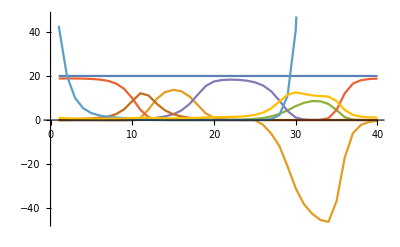

```mathematica
ListPlot[out[[2]],Joined->True]
```